```mathematica
2-2
```

0

# Ray's Argument

Nicholas Wheeler
16 August 2012

### Introduction

"Partitons of unity" (notebook dated 12 August) begins with discussion of random bisections of unity, and exposes an unanticipated problem: I found that two equally "natural" approaches to the production of random bisections led to populations that were statistically distinct.

FIRST PROCEDURE: {x, 1 - x} with x random on [0, 1].
    SECOND PROCEDURE: {x, y}/(x+y) with x,y random on [0, 1].

I took my problem to Ray Mayer on Monday the 13th, and when I returned to my office on the 15th I found a solution taped to my door.

### The first procedure is trivial

Assume that the random number x is uniformly distributed on the unit interval:

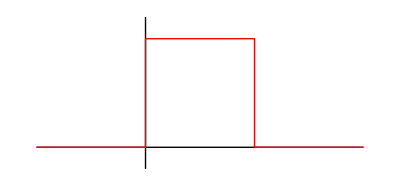

```mathematica
Graphics[{
Line[{{-1,0},{2,0}}],
Line[{{0,-.2},{0,1.2}}],
{Thick,Red,Line[{{-1,0},{0,0},{0,1},{1,1},{1,0},{2,0}}]}
}]
```

Then the probability that x ⩽ α (0 ⩽ α ⩽ 1) is just α, the shaded region in the following animated figure:

```mathematica
Framework1[α_]:=Graphics[{
Line[{{0,0},{1,0},{1,1},{0,1},{0,0}}],
Line[{{1.0,0},{1.2,0}}],
Line[{{0,1.0},{0,1.2}}],
Line[{{α,0},{α,1}}]
}]

Shaded1[α_]:=Graphics[{Opacity[.3],Blue,Polygon[{{0,0},{α,0},{α,1},{0,1}}]}]
```

```mathematica
Manipulate[Show[{Shaded1[α],Framework1[α]}],{α,0,1}]
```

The rate of growth is constant; the bisections are uniformly distributed.

### Ray's analysis of the second procedure

Write

{x/(x+y),y/(x+y)}={α,β}

and assume x and y to be uniformly/independently distributed on the unit square. Distinct values of x and y give rise to the same value of α (from which the β-value follows automatically: β = 1 - α). Those lie on a line:

y=(1-α)/α x

that passes through the points

{x,y}={0,0}
{x,y}={α/(1-α),1}

The α-line has

```mathematica
slope[α_]:=(1-α)/α
```

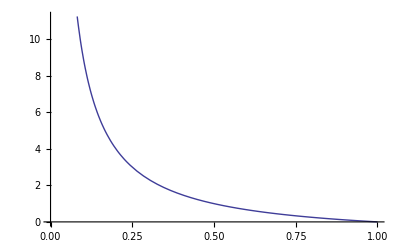

```mathematica
Plot[slope[α],{α,0,1}]
```

```mathematica
Framework2[α_]:=Graphics[{
Line[{{0,0},{1,0},{1,1},{0,1},{0,0}}],
Line[{{1.0,0},{1.2,0}}],
Line[{{0,1.0},{0,1.2}}],
Line[{{0,0},1.2{α/(1-α),1}}]
}]
```

```mathematica
Manipulate[Framework2[α],{α,0,1/2}]
```

The probability that α ⩽ a (0 ⩽ a ⩽ 1/2) is equal to the shaded area in the following figures:

```mathematica
Shaded2[a_]:=Graphics[{Opacity[.3],Blue,Polygon[{{0,0},{a/(1-a),1},{0,1}}]}]
```

```mathematica
Manipulate[Show[{Shaded2[a],Framework2[a]}],{a,0,1/2}]
```

REMARK: The idea extends all the way to a = 1. It is to avoid distractingly fussy graphics commands that I have truncated the demonstration at a = 1/2.

The shaded triangle has (for 0 ⩽ a  ⩽ 1/2)

```mathematica
area[a_]:=1/2 a/(1-a)
```

```mathematica
Simplify[D[area[a],a]]
```

1/(2 (-1+a)^2)

```mathematica
ProbDensity[a_]:=1/(2 (-1+a)^2)
```

```mathematica
ProbDensity[1/2]
```

2

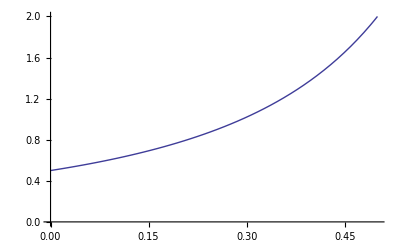

```mathematica
Plot[ProbDensity[a],{a,0,1/2},PlotRange->{0,2}]
```

```mathematica
Integrate[ProbDensity[a],{a,0,1/2}]
```

1/2

If 1/2 < a < 1 the shaded area becomes quadrilateral:

```mathematica
area2[a_]:=1-1/2(1-a)/a
```

```mathematica
Simplify[area2[a]]
```

3/2-1/(2 a)

```mathematica
Simplify[D[area2[a],a]]
```

1/(2 a^2)

```mathematica
ProbDensity2[a_]:=1/(2 a^2)
```

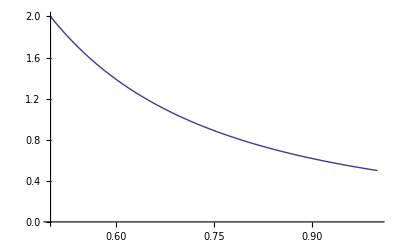

```mathematica
Plot[ProbDensity2[a],{a,1/2,1},PlotRange->{0,2}]
```

```mathematica
P[a_]:=Piecewise[{{ProbDensity[a],0<a<1/2},
{ProbDensity2[a],1/2<a<1}}]
```

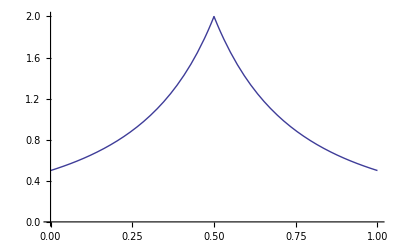

```mathematica
Plot[P[a],{a,0,1},PlotRange->{0,2}]
```

Here is the experimental result (different normalization) obtained in "Partitons of unity" (12 August 2012):

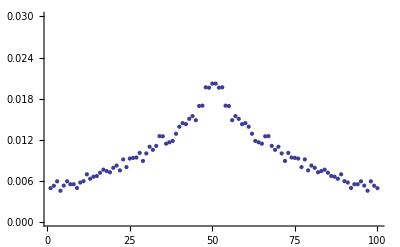

### Trisections and higher-order partitions

Can Ray's argument be carried to higher order? Look first to trisections. Write

{x/(x+y+z),y/(x+y+z),z/(x+y+z)}={α,β,γ=1-α-β}

The points {x, y, z} that contribute to a specified value of α lie on a plane (actually: on the part of a plane that lies interior to the unit cube):

(α-1)x+α y+α z==0

```mathematica
Manipulate[ContourPlot3D[(α-1)x+α y+α z==0,{x,0,1},{y,0,1},{z,0,1}],{α,0.1, 0.9}]
```

Ditto the points that contribute to a specified value of β. The points that contribute to {α, β}—which together assign value to γ (note that the requirement 0  < γ < 1 serves to constrain the values that can be assigned to α and β) lie therefore on the intersection of two planes:

```mathematica
Manipulate[ContourPlot3D[{(α-1)x+α y+α z==0,β x+(β-1) y+β z==0},{x,0,1},{y,0,1},{z,0,1}],{α,0.1,0.9},{β,0.1,0.9}]
```

Evidently 

prob[α < a, given β] = area swept out by the line of intersection as α advances from 0 to a

prob[β < b, given α] = area swept out by the line of intersection as β advances from 0 to b

conditional prob density[a givenb] = conditional prob density[b given a] = length of the line of intersection at {a, b}

One must, however, be careful to avoid impossible situations (a + b > 1), which are indicated by the  disappearance of the 3rd plane from the following figure:

```mathematica
Manipulate[ContourPlot3D[{(α-1)x+α y+α z==0,β x+(β-1) y+β z==0,(1-α-β) x+((1-α-β)-1) y+(1-α-β) z==0},{x,0,1},{y,0,1},{z,0,1}],{α,0.1,0.9},{β,0.1,0.9}]
```

The geometrical problem thus posed is, however, clearly intractable.

And for higher-order partitions one loses the possibility even of graphic representation of an even more intractable problem.

### Conclusions

Ray's elegant argument is special to the bisection problem. And it works only if the random numbers derive from the flat distribution.